## Define U_μ(x)

Check the result in Hamilton’s FFTLog notes

```mathematica
ClearAll[bigU];
bigU[mu_, x_] := N[2^x Gamma[(mu+1+x)/2]/Gamma[(mu+1-x)/2]]
```

```mathematica
Integrate[t^x BesselJ[μ, t],{t,0,Infinity}]
```

∫_0^∞ t^x BesselJ[μ,t]ⅆt

```mathematica
bigU[10, 0.5]
```

3.16424

```mathematica
NIntegrate[t^(1/2)BesselJ[10,t],{t,0,Infinity}, PrecisionGoal->10]
```

3.16424

## Define u_m(μ,q)

```mathematica
ClearAll[um];
um[m_, mu_, q_, kr0_, L_] := With[{fac= 2π m I/L}, kr0^-fac bigU[mu, q+fac]]
```

Test reality conditions

```mathematica
um[1, 0.5, 0.5, 1, 1]
```

2.43084-0.611705 ⅈ

```mathematica
um[-1, 0.5, 0.5, 1, 1]
```

2.43084+0.611705 ⅈ

## Fourier Transform Conditions

Odd n

```mathematica
tmp = RandomReal[1, 11]
```

{0.349062,0.396627,0.612739,0.829789,0.179998,0.713781,0.875786,0.678265,0.669506,0.771766,0.488263}

```mathematica
Fourier[tmp]
```

{1.9796+0. ⅈ,-0.190546-0.138018 ⅈ,-0.124668+0.100128 ⅈ,-0.241629-0.175937 ⅈ,0.202213+0.0548135 ⅈ,-0.0563153+0.142969 ⅈ,-0.0563153-0.142969 ⅈ,0.202213-0.0548135 ⅈ,-0.241629+0.175937 ⅈ,-0.124668-0.100128 ⅈ,-0.190546+0.138018 ⅈ}

```mathematica
tmp-InverseFourier[Fourier[tmp]]
```

{-2.22045×10^-16,5.55112×10^-17,1.11022×10^-16,1.11022×10^-16,2.22045×10^-16,-1.11022×10^-16,-1.11022×10^-16,2.22045×10^-16,0.,1.11022×10^-16,5.55112×10^-17}

Even n

```mathematica
tmp = RandomReal[1, 6]
```

{0.319843,0.42329,0.0152763,0.727567,0.192917,0.897497}

```mathematica
Fourier[tmp]
```

{1.05181+0. ⅈ,0.0606546-0.230463 ⅈ,0.115502-0.104852 ⅈ,-0.620667+0. ⅈ,0.115502+0.104852 ⅈ,0.0606546+0.230463 ⅈ}

```mathematica
ClearAll[ffreq];
ffreq[n_Integer]:= RotateLeft[Range[-Floor[n/2],Ceiling[n/2]-1] , Floor[n/2]]
```

## Gaussian Hankel Transforms - Brute Force

```mathematica
ClearAll[a, atilde];
a[r_] := Exp[-Log[r]^2/2]
```

```mathematica
atilde[k_] := k*NIntegrate[a[r] * BesselJ[-1/2, k*r], {r, 0, Infinity}, PrecisionGoal->5]
```

```mathematica
atilde[0.1]
```

0.663651

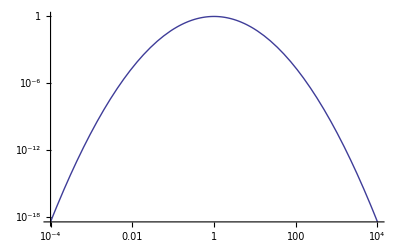

```mathematica
LogLogPlot[a[r], {r, 10^-4, 10^4}]
```

```mathematica
kvals = 10^Range[-3, 3, 0.1];
```

```mathematica
akarr = atilde/@ kvals;
```

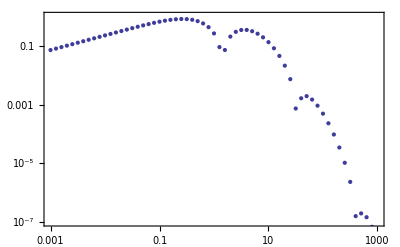

```mathematica
ListLogLogPlot[Transpose[{kvals, Abs[akarr]}], PlotRange->{{10^-3, 10^3}, {10^-7, 1}}, Frame->True]
```

## FFTLog - in steps

Start by defining the function (do this for the case of even N, so that we can test things out somewhat)

```mathematica
rvals = 10^(Range[1000]*0.008-4);
```

```mathematica
rvals[[500]]
```

1.

```mathematica
mvals=ffreq[Length[rvals]];
```

```mathematica
mvals[[499;;501]]
```

{498,499,-500}

```mathematica
arvals = a[rvals];
```

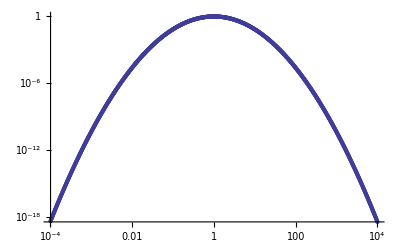

```mathematica
ListLogLogPlot[Transpose[{rvals, arvals}]]
```

```mathematica
cmvals = Fourier[arvals];
```

```mathematica
cmvals[[499;;501]]
```

{2.24693×10^-16+0. ⅈ,-2.24693×10^-16+4.49387×10^-16 ⅈ,0.+0. ⅈ}

Choose k_0= 1 and r_0=1 as our central values.

```mathematica
umvals = um[mvals,-1/2, 0, 1, 8Log[10]];
```

```mathematica
umvals[[499;;501]]
```

{-0.513617-0.85802 ⅈ,0.936484-0.350711 ⅈ,0.175666-0.98445 ⅈ}

```mathematica
umvals[[501]]=Re[umvals[[501]]]
```

0.175666

```mathematica
cmum = cmvals*umvals;
```

```mathematica
akvals = InverseFourier[cmum];
```

Now rvals is the same as kvals in this case ---

```mathematica
Max[Im[akvals]]
```

1.42498×10^-16

```mathematica
Min[Im[akvals]]
```

-1.06931×10^-16

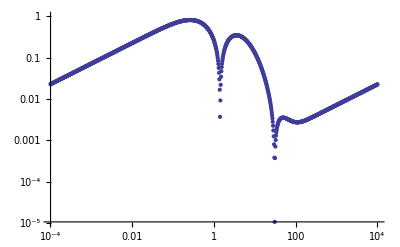

```mathematica
ListLogLogPlot[Transpose[{rvals, Abs[akvals]}]]
```

Note the effect of aliasing on the data.

Try a bigger range :

1.42174×10^-16

-1.46294×10^-16

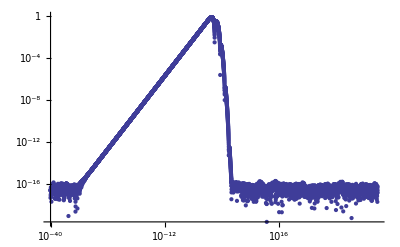

```mathematica
rvals = 10^(Range[10000]*0.008-40);
mvals=ffreq[Length[rvals]];
arvals = a[rvals];
cmvals = Fourier[arvals];
umvals = um[mvals,-1/2, 0, 1, 80Log[10]];
umvals[[5001]]=Re[umvals[[5001]]];
cmum = cmvals * umvals;
akvals = InverseFourier[cmum];
Max[Im[akvals]]
Min[Im[akvals]]
ListLogLogPlot[Transpose[{rvals, Abs[akvals]}]]
```

This has the same issue, although we’ve pushed the issue out to large scales.

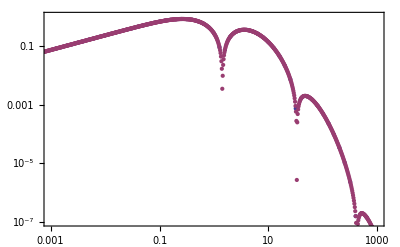

```mathematica
ListLogLogPlot[{Transpose[{kvals, Abs[akarr]}], Transpose[{rvals, Abs[akvals]}]}, PlotRange->{{10^-3, 10^3}, {10^-7, 1}}, Frame->True]
```

Bingo!!